```mathematica
c = 299792458;

Eg0 = 1;
Eg1 = 0.3464;
Eg2 = 0.0546;

M= 15; (*Azimuthal order*)
frf = 3*10^9; (*freq [Hz]*)
Lpipe = 0.25; (*length of pipe either side [m]*)
g = c/frf/2; (*total cavity length [m]*)
aMax = 0.0383;
Phase = 0; (*entry phase of particle [rad]*)

aArr =  {aMax/32,aMax/16,aMax/8,aMax/4,aMax/8*3,aMax/2,0.030};
aArr = {aMax/10, 2*aMax/10,3*aMax/10,4*aMax/10,5*aMax/10,6*aMax/10}
aArr = {0.01}

(*Note MATHEMATICA makes arrays of size +1.*)
NzSteps = 1000;  (*Default = 1000*)
Noffsets = 10; (* Default = 10*)
NkSteps = 1000; (*Default = 1000*)
UpperkFactor = 5000; (*Default = 5000*)
LSpacing = 500; (*How many longitudinal points to output*)

For[ll=0,ll<Length[aArr],ll++,
a = aArr[[ll+1]];


SF = 1; (*scale factor for x-offsets*)
MaxXoffset = SF*a; (*x-offsets*)

krf = 2*Pi*frf/c; 
L = g/2 + Lpipe;
z = N@Subdivide[-L,L,NzSteps];
PhaseArr = N@Subdivide[Phase,Phase,NzSteps];
kspecial = Pi/g/2;
klower1 = If[SF<=1,0, If[kspecial<=krf,kspecial,krf]];
kupper1 = krf;
klower2 = If[SF<=1,krf,If[kspecial<=krf,krf,kspecial]];
kupper2 = UpperkFactor*klower2;

xoffsets = N@Subdivide[0,MaxXoffset,Noffsets];
DeltaPzStat = {};
DeltaPzTime = {};
krange1 = N@Subdivide[klower1,kupper1,NkSteps];
krange2 = N@Subdivide[klower2,kupper2,UpperkFactor*NkSteps];
gJ = Eg*g/Sqrt[2*Pi]*Sinc[krange1*g/2]/BesselJ[M,√(krf^2-krange1^2)*a];
gI =  Eg*g/Sqrt[2*Pi]*Sinc[krange2*g/2]/BesselI[M,√(krange2^2-krf^2)*a];


datag=Join[Transpose@{krange1[[1;;-2]],gJ[[1;;-2]]},Transpose@{krange2,gI}];
(*ListLinePlot[datag,AxesLabel->{"k [1/m]","g(k) [V]"},GridLines->Automatic,PlotRange->{{0,1000},Full},PlotLabel-> StringTemplate["a = `1` [mm]"][a*1000]]*)
ListLinePlot[datag,Epilog->{Directive[AbsoluteThickness[2],Black],InfiniteLine[{krf, krf},{0,1}]},AxesLabel->{"k [1/m]","g(k) [V]"},GridLines->Automatic,PlotRange->{{0,1000},{-0.1,1.4}},PlotLabel-> StringTemplate["a = `1` [mm]"][a*1000]]

fung =  Interpolation[datag];
kfull = Join[krange1[[1;;-2]],krange2];
funk = Interpolation[kfull];
Export[StringTemplate["Z_m_`1`_a_`2`.mat"][M,a*1000], Table[z,{z,-L,L,L/LSpacing}],"MAT"];
Export[StringTemplate["k_m_`1`_a_`2`.mat"][M,a*1000], Table[k,{k,klower1,kupper1*20,kupper1/10000}],"MAT"]
Export[StringTemplate["g_m_`1`_a_`2`.mat"][M,a*1000], Table[fung[k],{k,klower1,kupper1*20,kupper1/10000}],"MAT"];

For[i=0,i<Length[xoffsets],i++,
(*i=3;*)
xoffset = xoffsets[[i+1]];
Print[xoffset];


EzJ = g/Pi*NIntegrate[Sinc[k*g/2]*(Eg0*BesselJ[0,√(krf^2-k^2)*xoffset]/BesselJ[0,√(krf^2-k^2)*a]+Eg1*BesselJ[1,√(krf^2-k^2)*xoffset]/BesselJ[1,√(krf^2-k^2)*a]+Eg2*BesselJ[2,√(krf^2-k^2)*xoffset]/BesselJ[2,√(krf^2-k^2)*a])*Cos[k*z],{k,klower1,kupper1}];
EzI = g/Pi*NIntegrate[Sinc[k*g/2]*(Eg0*BesselI[0,√(k^2-krf^2)*xoffset]/BesselI[0,√(k^2-krf^2)*a]+Eg1*BesselI[1,√(k^2-krf^2)*xoffset]/BesselI[1,√(k^2-krf^2)*a]+Eg2*BesselI[2,√(k^2-krf^2)*xoffset]/BesselI[2,√(k^2-krf^2)*a])*Cos[k*z],{k,klower2,kupper2}];
EzT = (EzJ+EzI);

dataT=Transpose@{z,EzT};
dataJ=Transpose@{z,EzJ};
  dataI=Transpose@{z,EzI};

TimeArray = Cos[2*Pi*frf*z/c+PhaseArr];
dataTTime = Transpose@{z,EzT*TimeArray};

funStat = Interpolation[dataT]; 
AppendTo[DeltaPzStat, NIntegrate[funStat[z],{z,-L,L}]];

funTime = Interpolation[dataTTime]; 
AppendTo[DeltaPzTime, NIntegrate[funTime[z],{z,-L,L}]];

SetDirectory[FileNameJoin[{NotebookDirectory[], "/Outputs"}]];
Export[StringTemplate["Ez_m_`1`_a_`2`_r_`3`.mat"][M,a*1000,xoffset*1000], Table[funStat[z],{z,-L,L,L/LSpacing}],"MAT"];

Plot[funStat[z],{z,-L,L},AxesLabel->{"z [m]","Ez(t=0)"},PlotRange->Full]
Plot[funTime[z],{z,-L,L},AxesLabel->{"z [m]","Ez(t)"},PlotRange->Full]


(*ListLinePlot[{dataT,dataJ,dataI}]*)
ListLinePlot[{dataTTime, dataT,dataJ,dataI},AxesLabel->{"z [m]","E_z [V/m]"}, PlotLegends ->{"E_z(t)","E_z","E_z (k<k_rf)","E_z (k>k_rf)" },GridLines->Automatic,PlotLabel-> StringTemplate["a = `1` [mm]; r = `2` [mm]"][a*1000,xoffset*1000],PlotRange->Full,Epilog->{Directive[AbsoluteThickness[2],Black],{InfiniteLine[{g/2, g/2},{0,1}],InfiniteLine[{-g/2, -g/2},{0,1}]}}]
(*ListLinePlot[dataT]
ListLinePlot[dataJ]
ListLinePlot[dataI]*)
(*ListLinePlot[dataTTime]*)
(*]*)

]


DeltaPzStat
DeltaPzTime 

dataPzStat=Transpose@{xoffsets,DeltaPzStat};
dataPzTime = Transpose@{xoffsets,DeltaPzTime};

funPzStat = Interpolation[dataPzStat];
funPzTime = Interpolation[dataPzTime];

Plot[funPzStat[xoffsets],{xoffsets,0,MaxXoffset},PlotLabel->"Pz Static Smooth"]
Plot[funPzStat'[xoffsets]/(2*Pi*frf),{xoffsets,0,MaxXoffset},PlotLabel->"Px Static Smooth"]
Plot[funPzTime[xoffsets],{xoffsets,0,MaxXoffset},PlotLabel->"Pz Time Smooth"]
Plot[funPzTime'[xoffsets]/(2*Pi*frf),{xoffsets,0,MaxXoffset},PlotLabel->"Px Time Smooth"]

SetDirectory[FileNameJoin[{NotebookDirectory[], "/Outputs"}]];
Export[StringTemplate["Offsets_m_`1`_a_`2`.mat"][M,a*1000], Table[xoffsets,{xoffsets,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PzStatic_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzStat[xoffsets],{xoffsets,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PxStatic_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzStat'[xoffsets]/(2*Pi*frf),{xoffsets,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PzTime_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzTime[xoffsets],{xoffsets,0,MaxXoffset,MaxXoffset/100}],"MAT"]
Export[StringTemplate["PxTime_m_`1`_a_`2`.mat"][M,a*1000], Table[funPzTime'[xoffsets]/(2*Pi*frf),{xoffsets,0,MaxXoffset,MaxXoffset/100}],"MAT"]
//Print]
```

{0.00383,0.00766,0.01149,0.01532,0.01915,0.02298}

{0.01}

General::munfl: 1/(4.49612×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(4.49894×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(4.50177×10^307) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

$Aborted

Offsets_m_0_a_19.0.mat PxStatic_m_0_a_19.0.mat PxTime_m_0_a_19.0.mat PzStatic_m_0_a_19.0.mat PzTime_m_0_a_19.0.mat

0.019

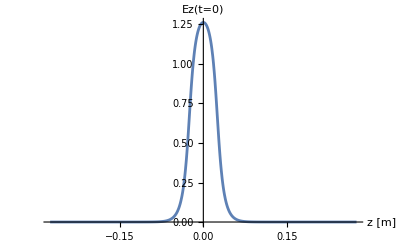
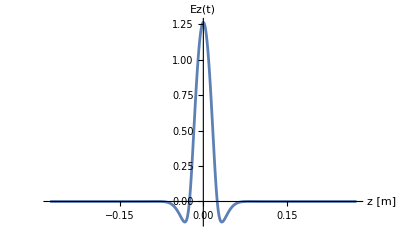
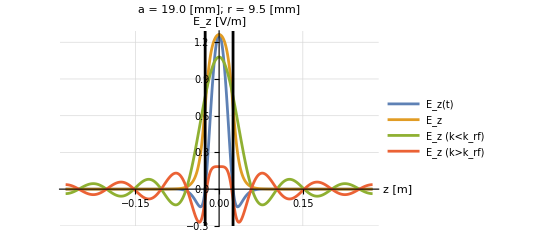

0.0095

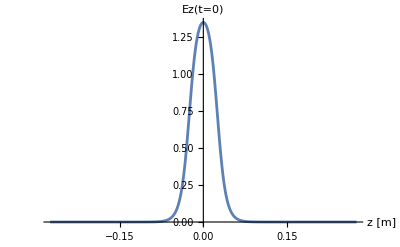
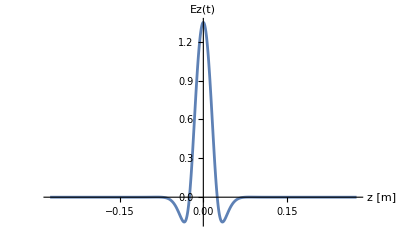
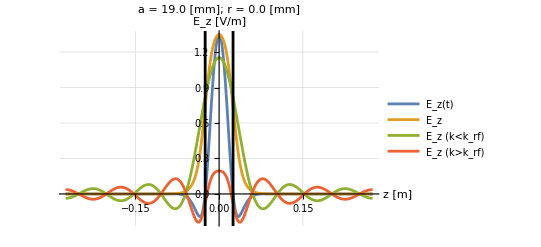

0.

Offsets_m_0_a_3.8.mat PxStatic_m_0_a_3.8.mat PxTime_m_0_a_3.8.mat PzStatic_m_0_a_3.8.mat PzTime_m_0_a_3.8.mat

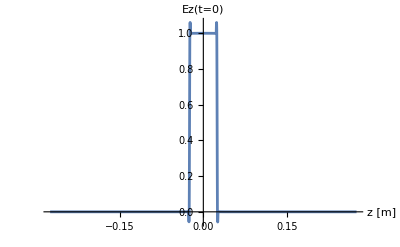
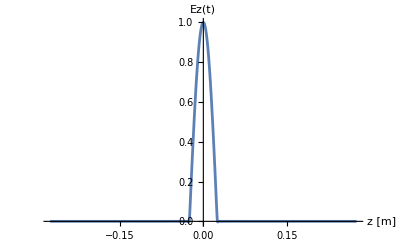
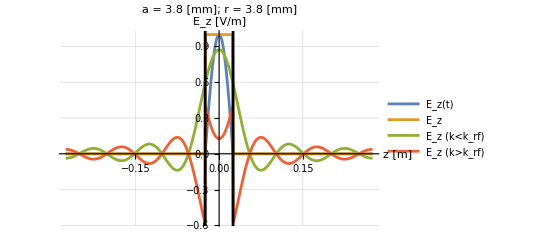

0.0038

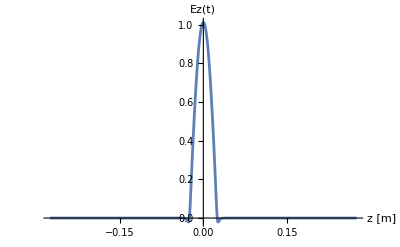
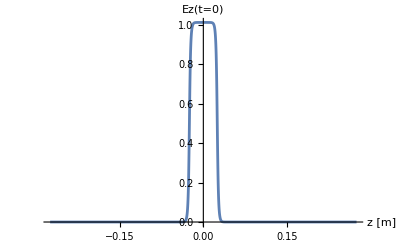
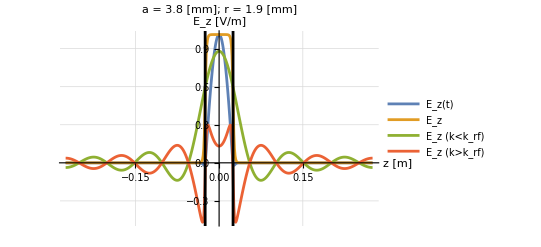

0.0019

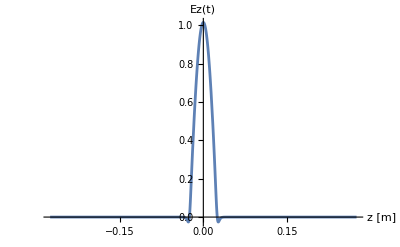
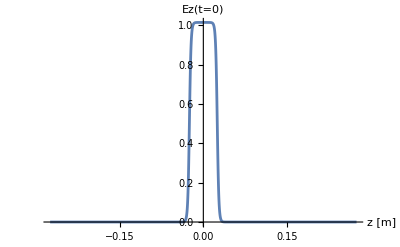
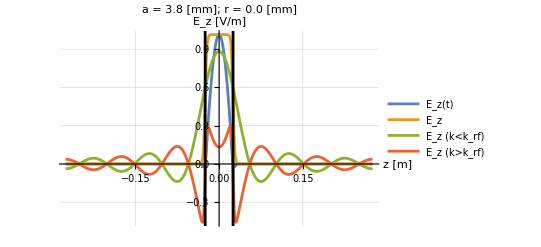

0.

Offsets_m_0_a_19.0.mat PxStatic_m_0_a_19.0.mat PxTime_m_0_a_19.0.mat PzStatic_m_0_a_19.0.mat PzTime_m_0_a_19.0.mat

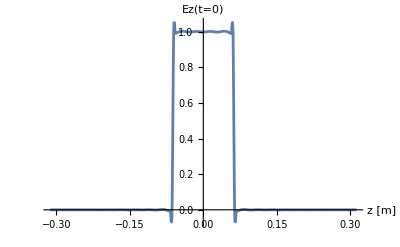
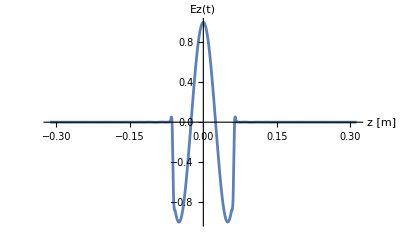
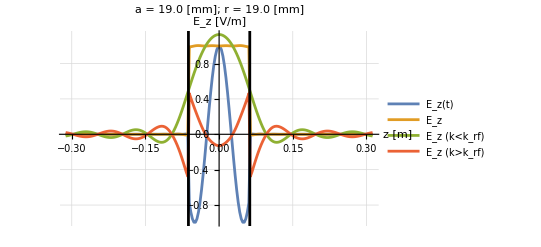

0.019

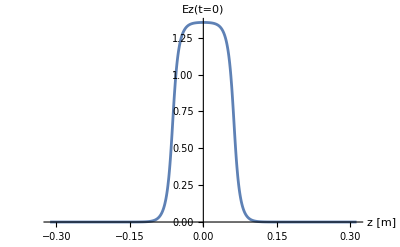
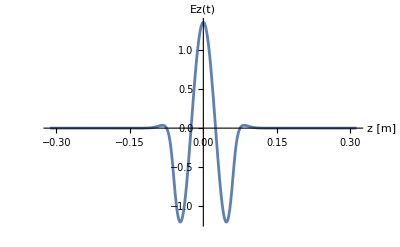
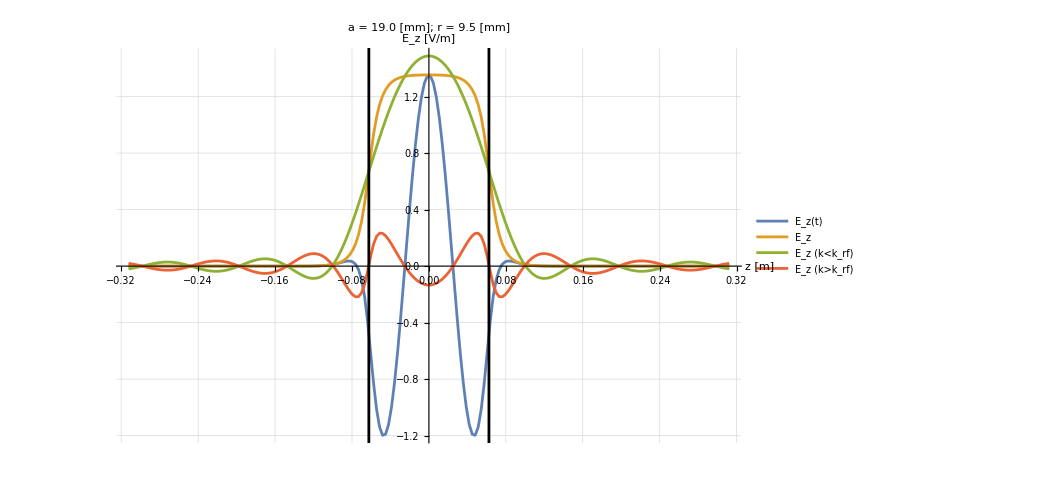

0.0095

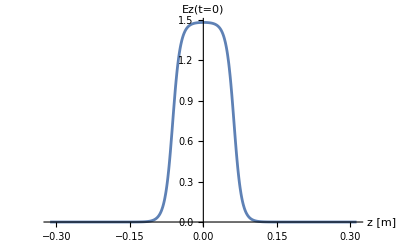
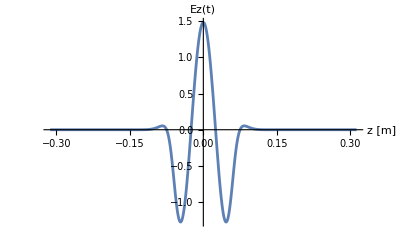
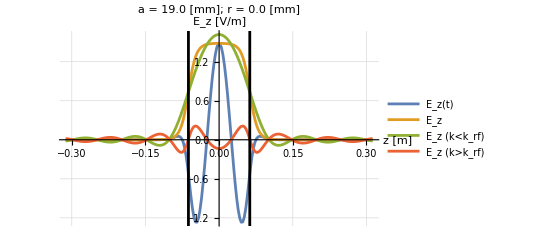

0.

Offsets_m_0_a_30.0.mat PxStatic_m_0_a_30.0.mat PxTime_m_0_a_30.0.mat PzStatic_m_0_a_30.0.mat PzTime_m_0_a_30.0.mat

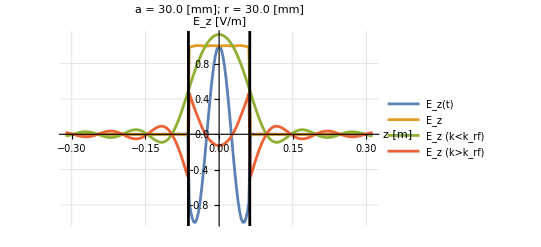
-Graphics- -Graphics- -Graphics-

0.03

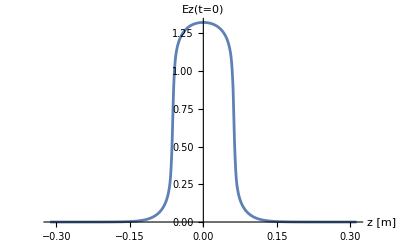
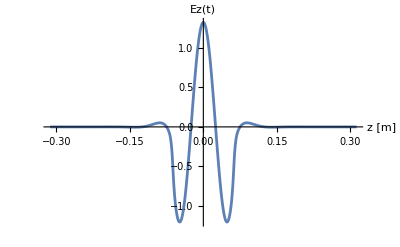
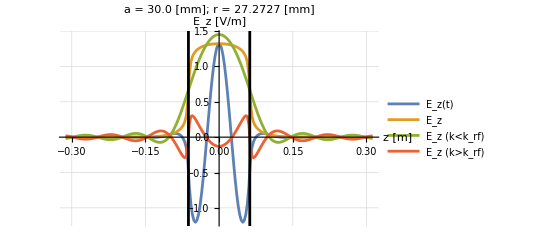

0.0272727

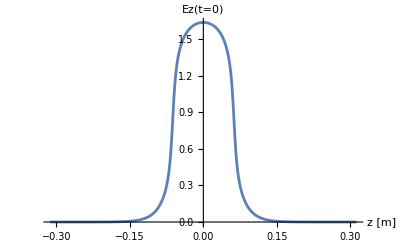
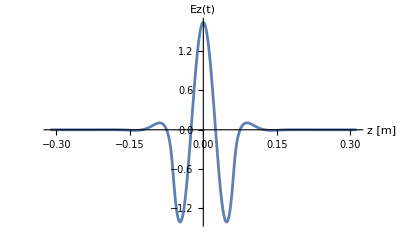
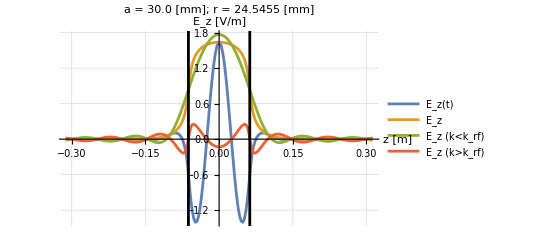

0.0245455

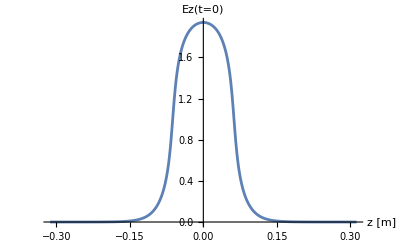
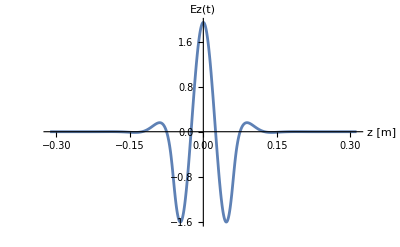
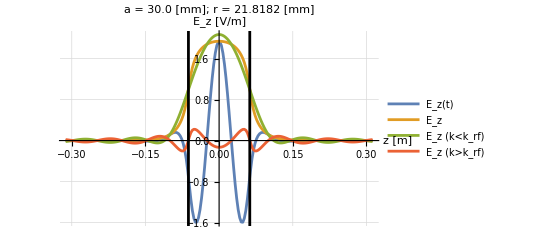

0.0218182

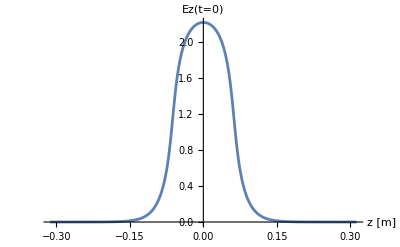
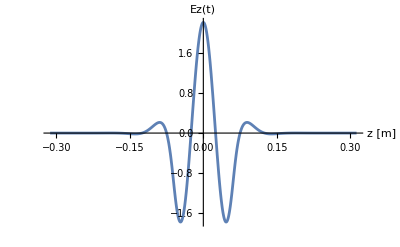
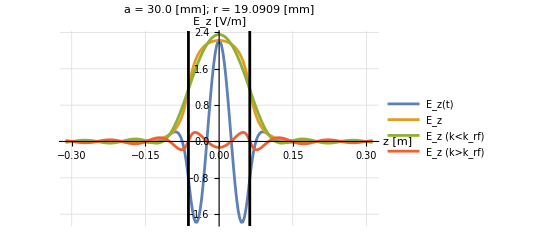

0.0190909

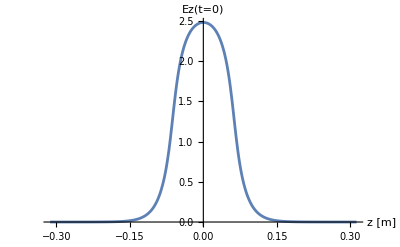
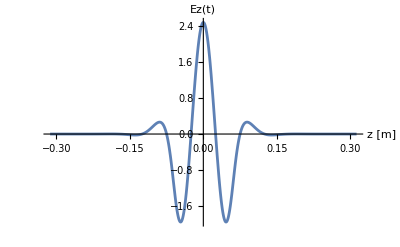
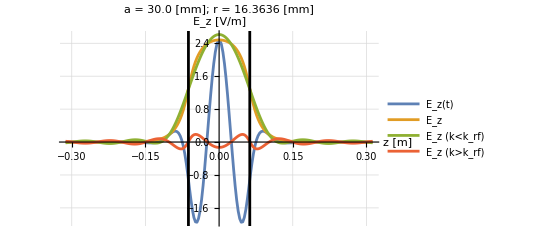

0.0163636

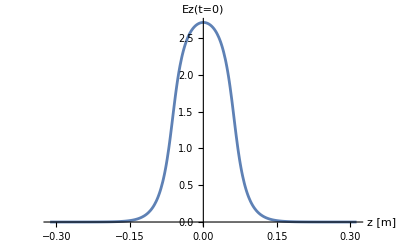
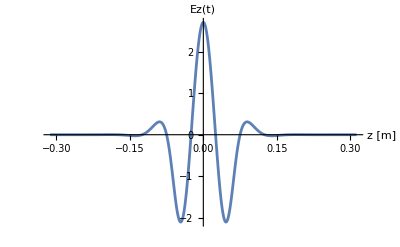
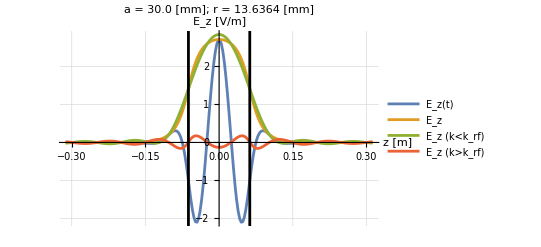

0.0136364

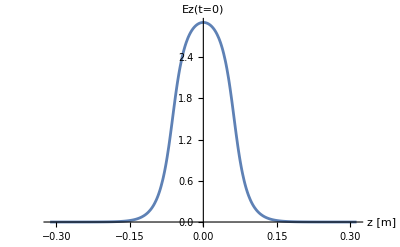
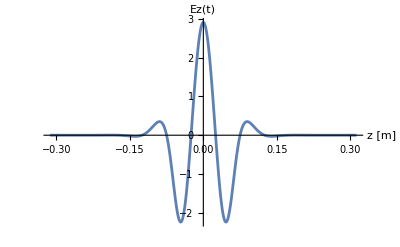
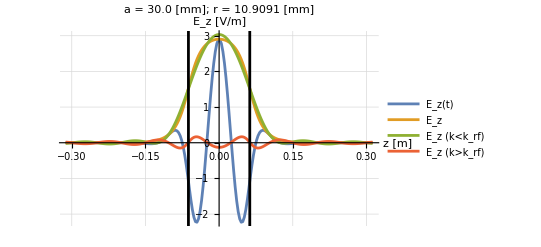

0.0109091

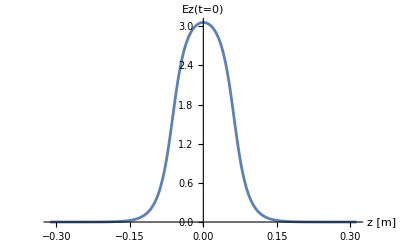
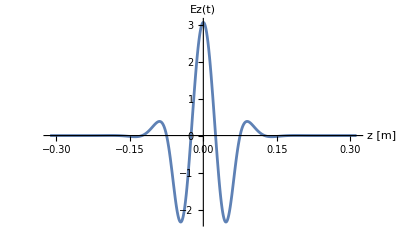
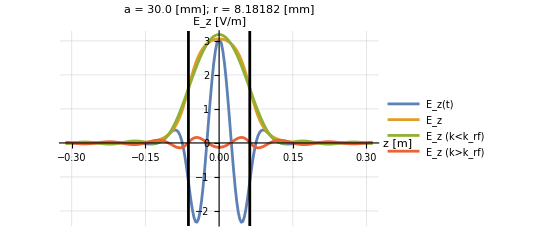

0.00818182

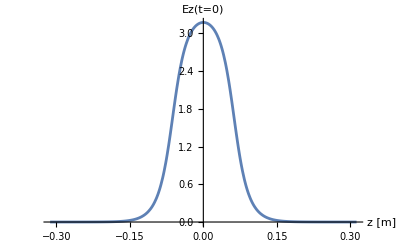
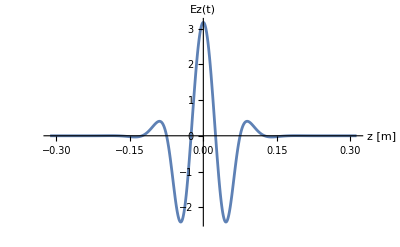
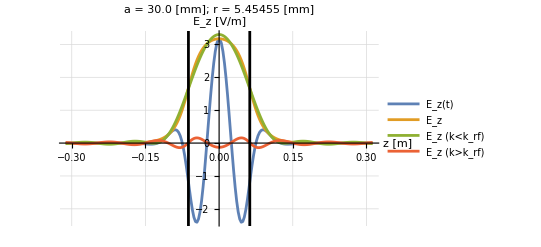

0.00545455

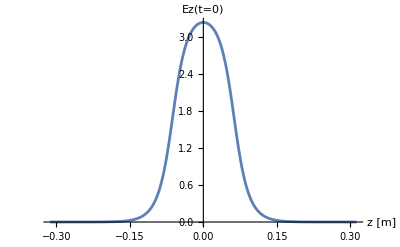
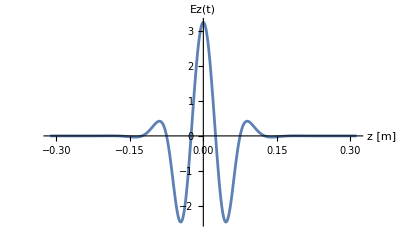
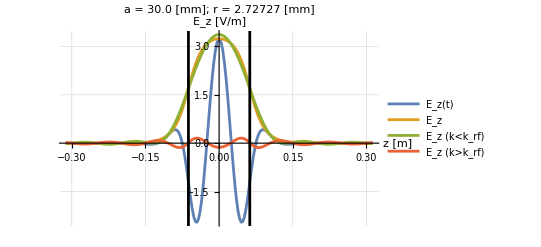

0.00272727

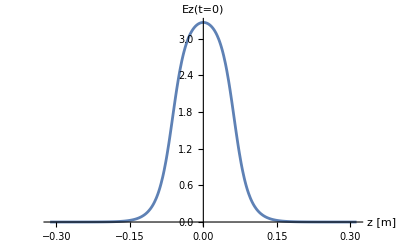
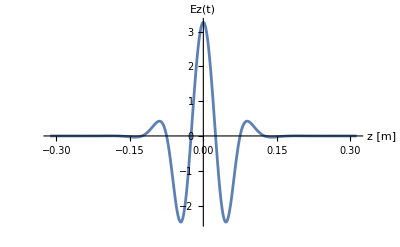
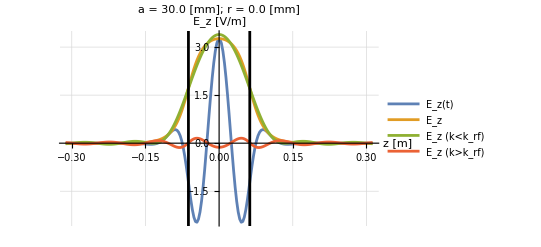

0.

Offsets_m_0_a_19.0.mat PxStatic_m_0_a_19.0.mat PxTime_m_0_a_19.0.mat PzStatic_m_0_a_19.0.mat PzTime_m_0_a_19.0.mat

-Graphics- -Graphics- -Graphics-

0.019

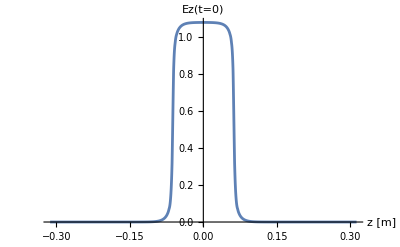
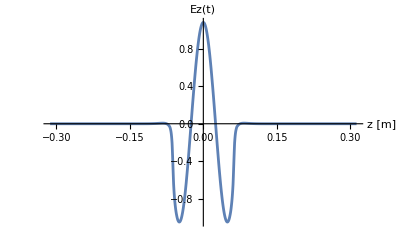
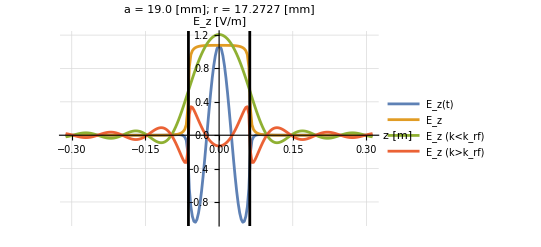

0.0172727

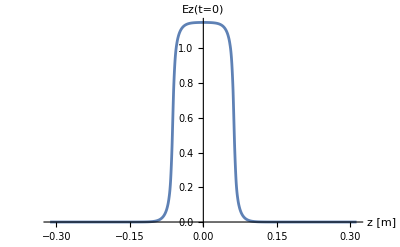
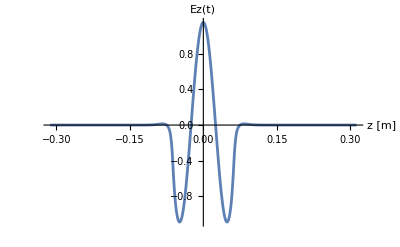
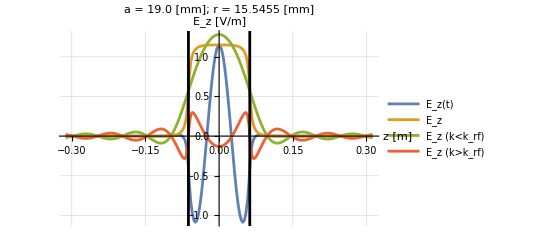

0.0155455

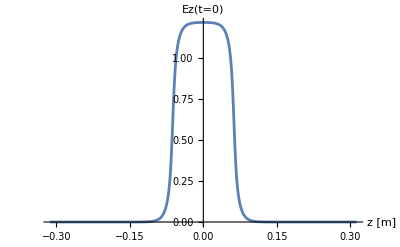
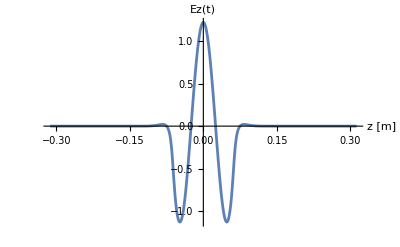
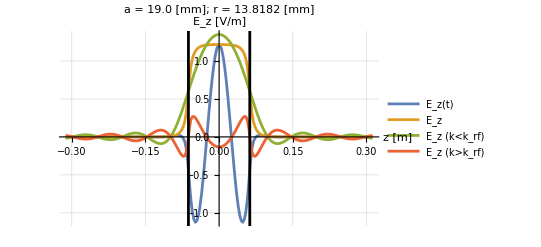

0.0138182

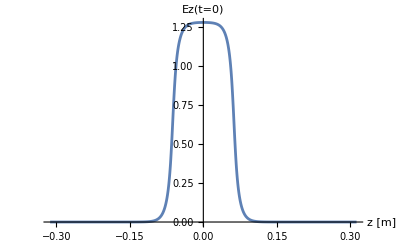
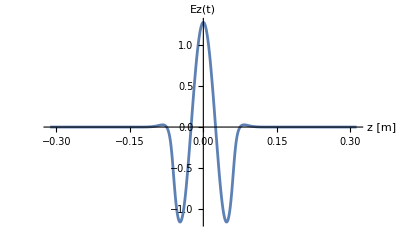
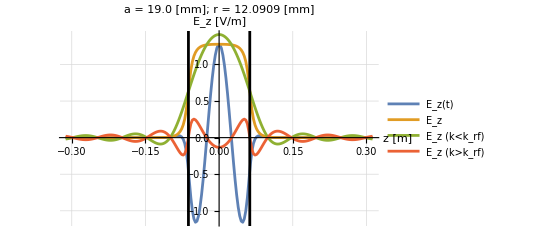

0.0120909

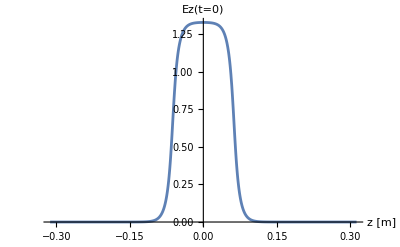
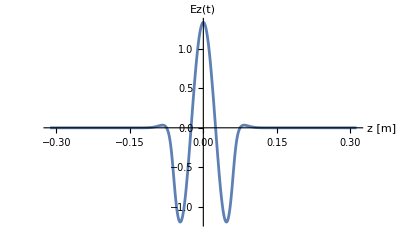
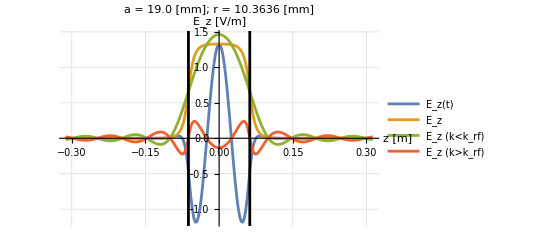

0.0103636

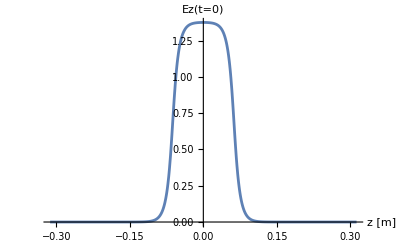
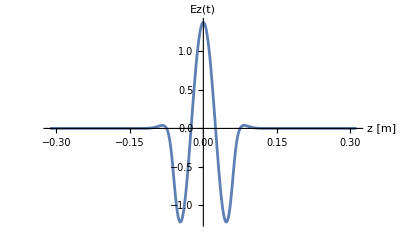
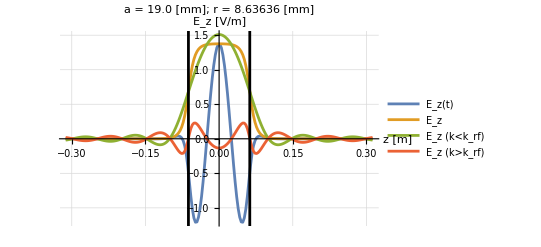

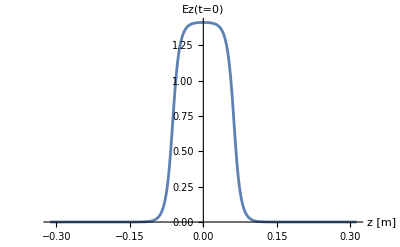
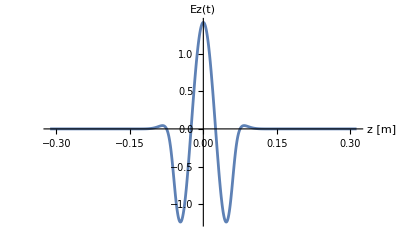
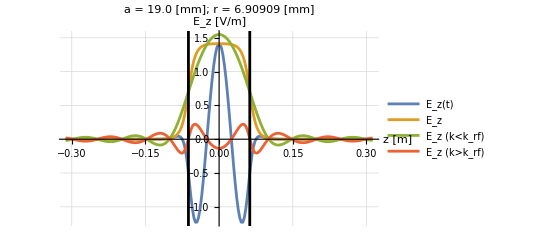

0.00690909

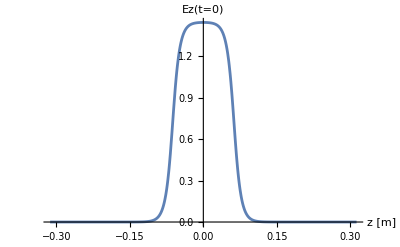
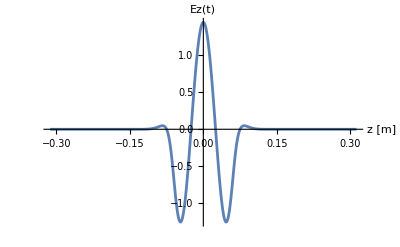
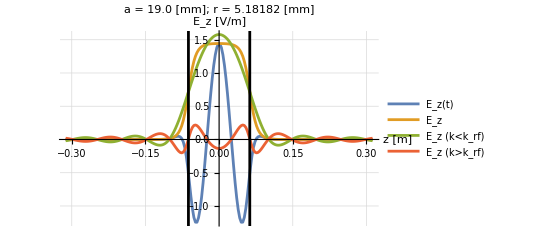

0.00518182

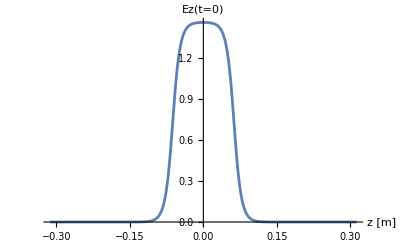
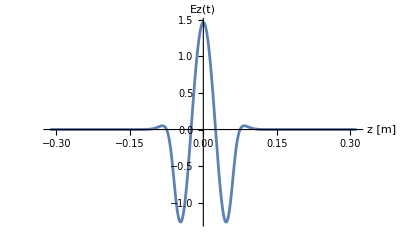
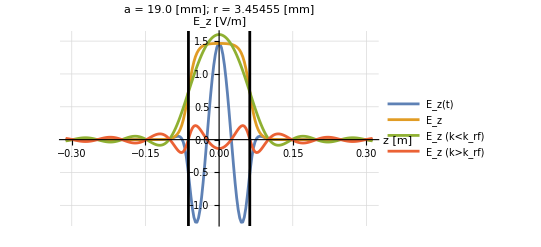

0.00345455

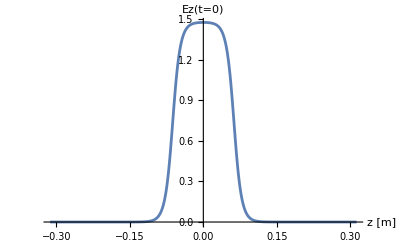
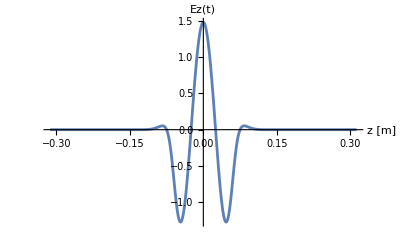
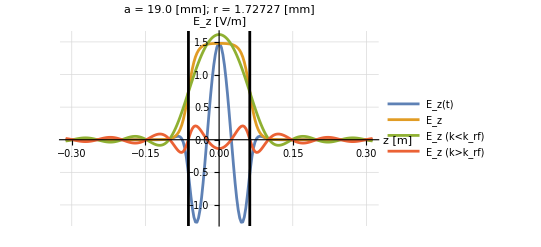

0.00172727

-Graphics- -Graphics- -Graphics-

0.

Offsets_m_0_a_14.25.mat PxStatic_m_0_a_14.25.mat PxTime_m_0_a_14.25.mat PzStatic_m_0_a_14.25.mat PzTime_m_0_a_14.25.mat

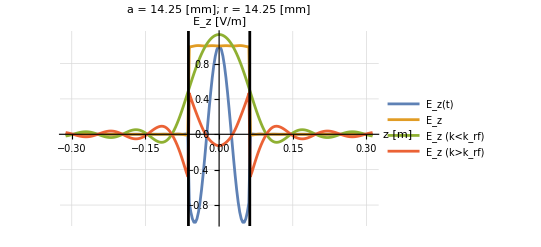
-Graphics- -Graphics- -Graphics-

0.01425

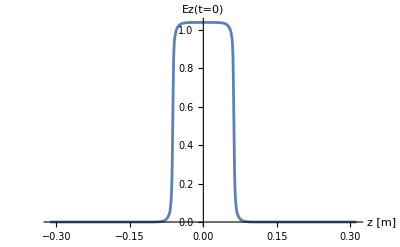
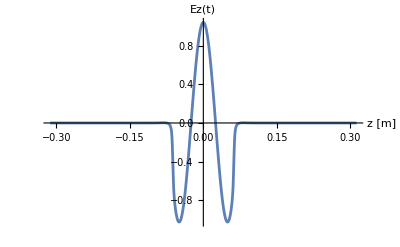
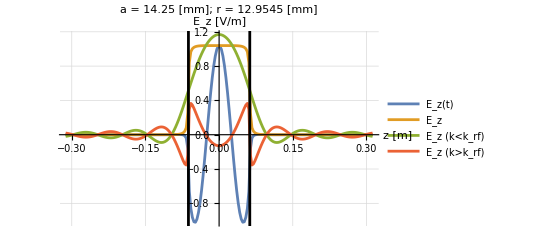

0.0129545

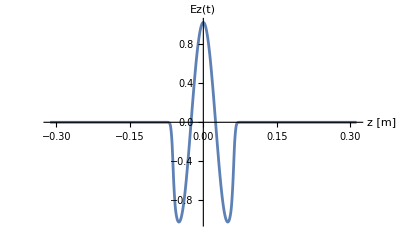
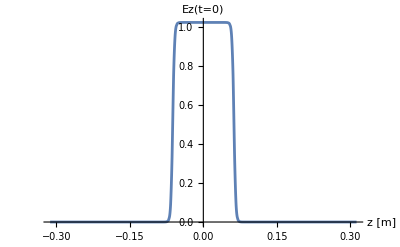
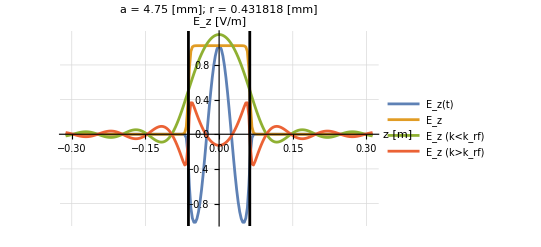

0.000431818

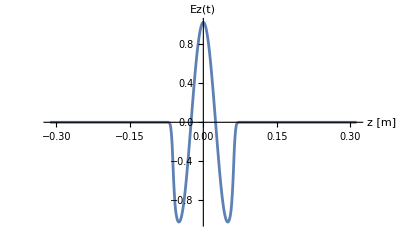
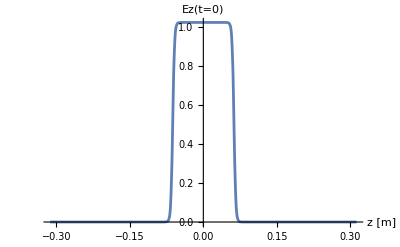
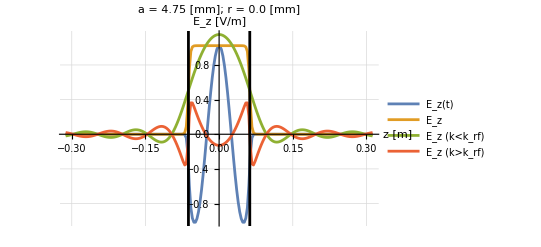

0.

Offsets_m_0_a_2.375.mat PxStatic_m_0_a_2.375.mat PxTime_m_0_a_2.375.mat PzStatic_m_0_a_2.375.mat PzTime_m_0_a_2.375.mat

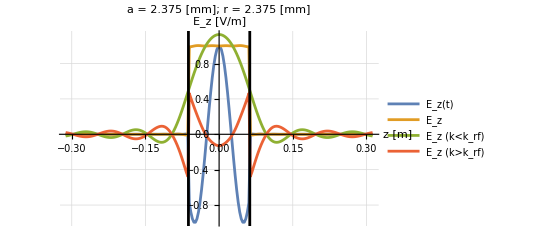
-Graphics- -Graphics- -Graphics-

0.002375

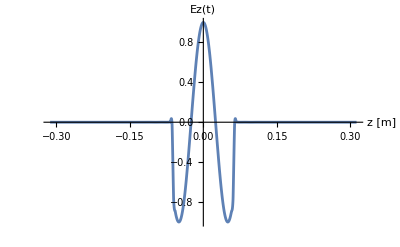
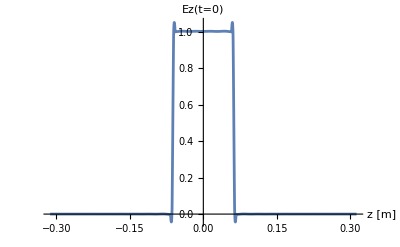
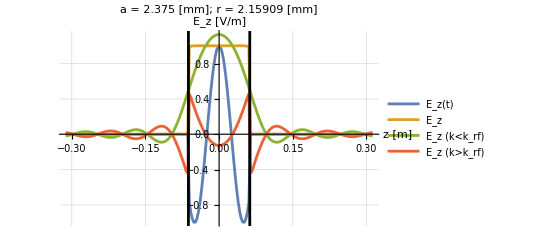

0.00215909

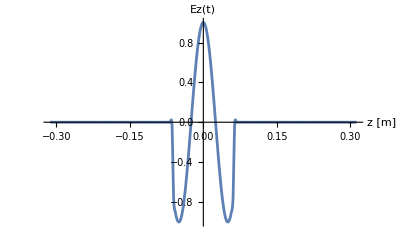
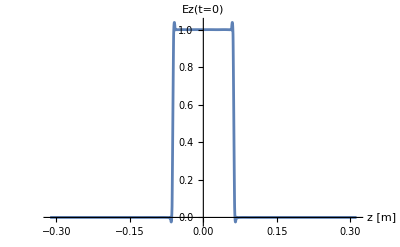
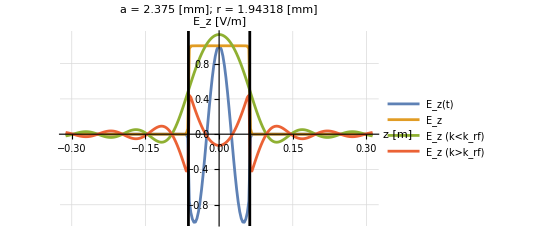

0.00194318

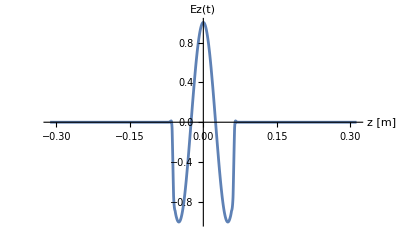
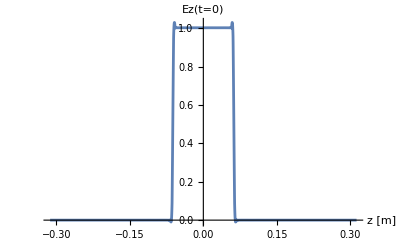
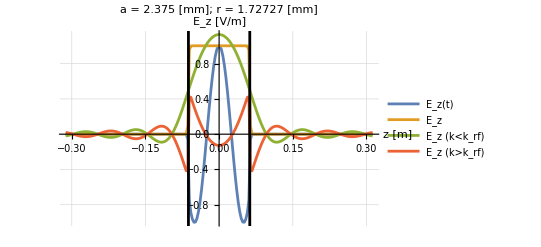

0.00172727

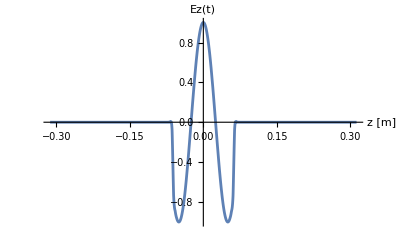
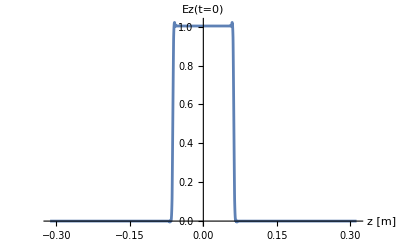
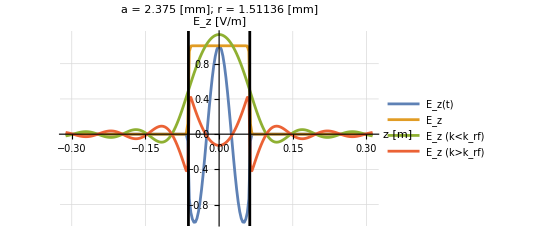

0.00151136

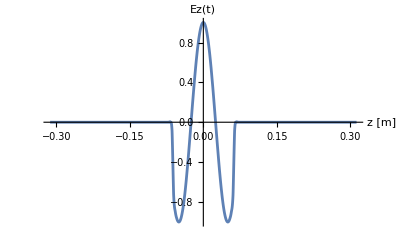
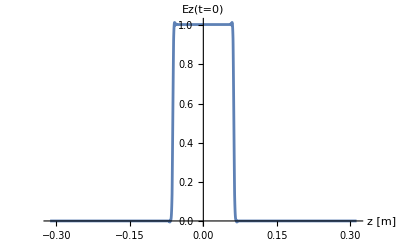
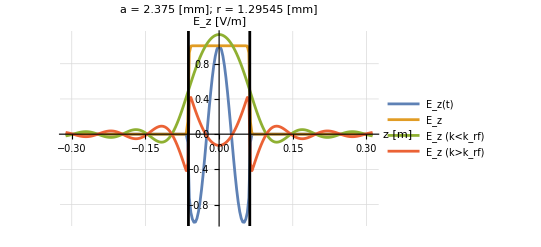

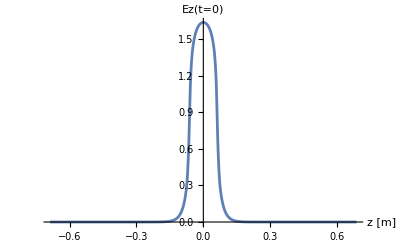
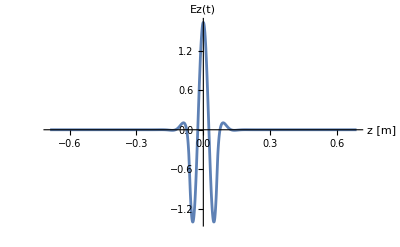
-Graphics- -Graphics- -Graphics-

0.0245455

-Graphics- -Graphics- -Graphics-

0.0218182

-Graphics- -Graphics- -Graphics-

0.0190909

-Graphics- -Graphics- -Graphics-

0.0163636

-Graphics- -Graphics- -Graphics-

0.0136364

-Graphics- -Graphics- -Graphics-

0.0109091

-Graphics- -Graphics- -Graphics-

0.00818182

-Graphics- -Graphics- -Graphics-

0.00545455

0.00272727

0.

Offsets_m_0_a_19.0.mat PxStatic_m_0_a_19.0.mat PxTime_m_0_a_19.0.mat PzStatic_m_0_a_19.0.mat PzTime_m_0_a_19.0.mat

0.019

0.0172727

-Graphics- -Graphics- -Graphics-

0.0155455

-Graphics- -Graphics- -Graphics-

0.0138182

-Graphics- -Graphics- -Graphics-

0.0120909

-Graphics- -Graphics- -Graphics-

0.0103636

-Graphics- -Graphics- -Graphics-

0.00863636

-Graphics- -Graphics- -Graphics-

0.00690909

-Graphics- -Graphics- -Graphics-

0.00518182

-Graphics- -Graphics- -Graphics-

0.00345455

-Graphics- -Graphics- -Graphics-

0.00172727

-Graphics- -Graphics- -Graphics-

0.0095

-Graphics- -Graphics- -Graphics-

0.00863636

-Graphics- -Graphics- -Graphics-

0.00777273

-Graphics- -Graphics- -Graphics-

0.00690909

-Graphics- -Graphics- -Graphics-

0.00604545

-Graphics- -Graphics- -Graphics-

0.00518182

-Graphics- -Graphics- -Graphics-

0.00431818

-Graphics- -Graphics- -Graphics-

0.00345455

-Graphics- -Graphics- -Graphics-

0.00259091

-Graphics- -Graphics- -Graphics-

0.00172727

-Graphics- -Graphics- -Graphics-

0.000863636

-Graphics- -Graphics- -Graphics-

0.

Offsets_m_0_a_4.75.mat PxStatic_m_0_a_4.75.mat PxTime_m_0_a_4.75.mat PzStatic_m_0_a_4.75.mat PzTime_m_0_a_4.75.mat

-Graphics- -Graphics- -Graphics-

0.00475

-Graphics- -Graphics- -Graphics-

0.00431818

-Graphics- -Graphics- -Graphics-

0.00388636

```mathematica
NotebookDelete[Cells[EvaluationNotebook[],GeneratedCell->True]]
```

```mathematica
Plot[funStat[z],{z,-L,L},AxesLabel->{"z [m]","Ez(t=0)"},PlotRange->Full]
Plot[funTime[z],{z,-L,L},AxesLabel->{"z [m]","Ez(t)"},PlotRange->Full]
```

```mathematica
(*Print[datag];*)
(*SetDirectory[FileNameJoin[{NotebookDirectory[], "/Outputs"}]];
Export[StringTemplate["Offsets_m_`1`_a_`2`.dat"][M,a*1000], Table[xoffsets,{xoffsets,0,MaxXoffset,MaxXoffset/100}]]*)
(*Plot[funPzTime'[xoffsets]/(2*Pi*frf*10^6),{xoffsets,0,MaxXoffset},PlotLabel->"Px Time Smooth"]*)
```

```mathematica
Print[kupper2]
Plot[fung[k],{k,0,kupper2},PlotRange->{{0,300},{-0.1,0.4}}]
```

```mathematica
Export[StringTemplate["k_m_`1`_a_`2`.mat"][M,a*1000], Table[k,{k,klower1,kupper2,(kupper2-klower1)/1000}],"MAT"]
```

```mathematica
Print[Table[fung[k],{k,0,kupper2,(kupper2-0)/5000}]]
```

```mathematica
Print[Table[fung[k],{k,0,kupper2,(kupper2-0)/5000}]]
```

```mathematica
Print[krange1]
Print[krange2]
```

```mathematica
(*ListLinePlot[{dataPzStat,dataPzTime},PlotLabel->"Pz"]
ListLinePlot[dataPzTime,PlotLabel->"Pz Time"]
ListLinePlot[{dataPxStat,dataPxTime},PlotLabel->"Px"]
ListLinePlot[dataPxTime,PlotLabel->"Px Time"]*)
```